## Markov Partition and Symbolic Dynamics

```mathematica
Hyperlink["http://arxiv.org/abs/math-ph/0204022"]
```

### Initialization

```mathematica
g[{i_Integer,j_Integer},{x_,y_}] := {x+i,y+j}
```

```mathematica
M := {{1,1},{1,2}}
𝔉[{x_,y_}] := M.{x,y}
F[{x_,y_}]:= Mod[𝔉[{x,y}],1]
```

```mathematica
invM:=Inverse[M]
inv𝔉[{x_,y_}]:=invM.{x,y}
invF[{x_,y_}] := Mod[inv𝔉[{x,y}],1]
```

```mathematica
halfM := {{0,1},{1,1}}
half𝔉[{x_,y_}]:=halfM.{x,y}
halfF[{x_,y_}] := Mod[half𝔉[{x,y}],1]
invHalfM := Inverse[halfM]
invHalf𝔉[{x_,y_}]:=invHalfM.{x,y}
halfF[{x_,y_}] := Mod[invHalf𝔉[{x,y}],1]
```

```mathematica
σDef:=σ->(3+Sqrt[5])/2
ϕDef:= ϕ->(1+Sqrt[5])/2
```

```mathematica
randomPoints = Partition[Table[{RandomReal[1],RandomReal[1]},{i, 0, 100}, {j,0, 100}]//Flatten,2];
```

### Two-Cell Partition

The action of the fundamental group on stable and unstable manifolds determines the stable and unstable manifolds on the torus.

```mathematica
um[i_,j_,x_] := ϕ (x+i) + j
sm[i_,j_,x_]:= - (x+i)/ϕ+j
```

```mathematica
um[i,j,x]/.ϕDef
sm[i,j,x]/.ϕDef
```

j+1/2 (1+√5) (i+x)

j+(2 (-i-x))/(1+√5)

```mathematica
Clear[x0,y0,x1,y1]
```

Finding where the unstable manifold crosses the homotopy loop x = 0 or 1

```mathematica
Solve[um[i,j,0]== y0,y0]
Solve[um[i,j,1]== y1,y1]
```

{{y0→j+i ϕ}}

{{y1→j+ϕ+i ϕ}}

```mathematica
y0um[i_,j_] := ϕ i + j
y1um[i_,j_]:= ϕ (i+1) +j
```

Finding where the unstable manifold crosses the homotopy loop y = 0 or 1

```mathematica
Solve[um[i,j,x0]== 0,x0]
Solve[um[i,j,x1]== 1,x1]
```

{{x0→(-j-i ϕ)/ϕ}}

{{x1→(1-j-i ϕ)/ϕ}}

```mathematica
x0um[i_,j_]:= -i-j/ϕ
x1um[i_,j_]:= -i-(j-1)/ϕ
```

Finding where the stable manifold crosses the homotopy loop x = 0 or 1

```mathematica
Solve[sm[i,j,0]== y0,y0]
Solve[sm[i,j,1]== y1,y1]
```

{{y0→(-i+j ϕ)/ϕ}}

{{y1→(-1-i+j ϕ)/ϕ}}

```mathematica
y0sm[i_,j_]:= -i/ϕ+j
y1sm[i_,j_]:= -(i+1)/ϕ+j
```

Finding where the stable manifold crosses the homotopy loop y = 0 or 1

```mathematica
Solve[sm[i,j,x0]== 0,x0]
Solve[sm[i,j,x1]== 1,x1]
```

{{x0→-i+j ϕ}}

{{x1→-i-ϕ+j ϕ}}

```mathematica
x0sm[i_,j_]:= -i+ϕ j
x1sm[i_,j_]:= -i+ϕ (j-1)
```

The distance of two points in the covering space.

```mathematica
distance[{x1_,y1_},{x2_,y2_}] := Sqrt[(x1-x2)(x1-x2)+(y1-y2)(y1-y2)]
```

Confirming that the map expands the unstable manifold by a factor of σ

```mathematica
u0 = distance[{0,0},{1,um[0,0,1]}]
u1 = distance[{0,0},𝔉[{1,um[0,0,1]}]]//Simplify
Sqrt[Factor[u1^2]/Factor[u0^2]]
%/.{ϕ-> σ-1}//Simplify
%/.σDef//Simplify
%^2 == Expand[σ^2/.σDef]
```

√(1+ϕ^2)

√(2+6 ϕ+5 ϕ^2)

√((2+6 ϕ+5 ϕ^2)/(1+ϕ^2))

√((1-4 σ+5 σ^2)/(2-2 σ+σ^2))

√(1/2 (7+3 √5))

True

Confirming that the map contracts the stable manifold by a factor of 1/σ

```mathematica
s0 = distance[{0,0},{1,sm[0,0,1]}]
s1 = distance[{0,0},𝔉[{1,sm[0,0,1]}]]
Sqrt[Simplify[s1^2]/Simplify[s0^2]]
%/.{ϕ-> σ-1}//Simplify
%/.σDef//Simplify
%^2 == Expand[1/σ^2/.σDef]
```

√(1+1/ϕ^2)

√((-1+1/ϕ)^2+(-1+2/ϕ)^2)

√((2+5/ϕ^2-6/ϕ)/(1+1/ϕ^2))

√((13-10 σ+2 σ^2)/(2-2 σ+σ^2))

√(1/2 (7-3 √5))

True

Constructing two rectangles in the universal covering space that completely cover the fundamental domain and that are defined by segments of stable and unstable manifolds.

Note that the points (0,0), (0,1), (1,0) and (1,1) of the universal covering are all identified to (0,0) on the torus. Therefore the stable manifold line going through (0,0) and the one going through (1,1) are identified as well as the unstable manifold line going through (0,0) and the one going through (0,1).

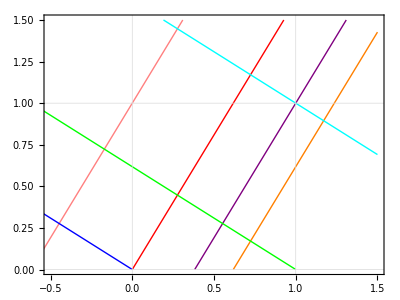

```mathematica
Plot[{um[0,0,x]/.ϕDef//N,um[0,1,x]/.ϕDef//N,um[0,-1,x]/.ϕDef//N,um[-1,1,x]/.ϕDef//N,sm[0,0,x]/.ϕDef//N,sm[-1,1,x]/.ϕDef//N,sm[-1,0,x]/.ϕDef//N}, {x,-1,1.5},PlotStyle->{Red,Pink,Orange,Purple,Blue,Cyan,Green},Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-0.5,1.5},{0,1.5}}, AspectRatio->Automatic,GridLines -> {{0,1},{0,1}}]
```

The first rectangle is delimited by the stable manifolds going through (0,0) and (1,1) and by the unstable manifolds going throgh (0,0) and (0,1).

```mathematica
vertexA = {};
Solve[um[0,0,x] == 0, x]
vertexA = Append[vertexA,{x/.%[[1]],0}];
Solve[sm[0,0,x] == um[0,1,x],x]
vertexA = Append[vertexA, {x/.%[[1]], sm[0,0,x]/.%[[1]]}];
Solve[sm[-1,1,x]== um[0,1,x],x]
vertexA = Append[vertexA, {x/.%[[1]],sm[-1,1,x]/.%[[1]]}];
Solve[um[0,0,x]== sm[-1,1,x], x]
vertexA = Simplify@Append[vertexA, {x/.%[[1]],sm[-1,1,x]/.%[[1]]}]
%/.ϕDef//Simplify
%//N
```

{{x→0}}

{{x→-ϕ/(1+ϕ^2)}}

{{x→1/(1+ϕ^2)}}

{{x→(1+ϕ)/(1+ϕ^2)}}

{{0,0},{-ϕ/(1+ϕ^2),1/(1+ϕ^2)},{1/(1+ϕ^2),(1+ϕ+ϕ^2)/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),(ϕ (1+ϕ))/(1+ϕ^2)}}

{{0,0},{-1/(√5),1/10 (5-√5)},{1/10 (5-√5),1+1/(√5)},{1/10 (5+√5),1/10 (5+3 √5)}}

{{0.,0.},{-0.447214,0.276393},{0.276393,1.44721},{0.723607,1.17082}}

The second rectangle is just the part of the torus that is not covered by the first rectangle and its images under the fundamental group.
This is the rectangle delimited by the stable manifolds going through (1,0) and (1,1) and the unstable manifolds going through (0,0) and (1,1).

```mathematica
vertexB = {};
Solve[um[0,0,x] == sm[-1,0,x], x]
vertexB = Append[vertexB,{x/.%[[1]],um[0,0,x]/.%[[1]]}];
Solve[um[0,0,x] == sm[-1,1,x],x]
vertexB= Append[vertexB, {x/.%[[1]], um[0,0,x]/.%[[1]]}];
Solve[sm[-1,1,x]== um[-1,1,x],x]
vertexB = Append[vertexB, {x/.%[[1]],sm[-1,1,x]/.%[[1]]}];
Solve[um[-1,1,x]== sm[-1,0,x], x]
vertexB= Simplify@Append[vertexB, {x/.%[[1]],sm[-1,0,x]/.%[[1]]}]
%/.ϕDef//Simplify
%//N
```

{{x→1/(1+ϕ^2)}}

{{x→(1+ϕ)/(1+ϕ^2)}}

{{x→1}}

{{x→(1-ϕ+ϕ^2)/(1+ϕ^2)}}

{{1/(1+ϕ^2),ϕ/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),(ϕ (1+ϕ))/(1+ϕ^2)},{1,1},{(1-ϕ+ϕ^2)/(1+ϕ^2),1/(1+ϕ^2)}}

{{1/10 (5-√5),1/(√5)},{1/10 (5+√5),1/10 (5+3 √5)},{1,1},{1-1/(√5),1/10 (5-√5)}}

{{0.276393,0.447214},{0.723607,1.17082},{1.,1.},{0.552786,0.276393}}

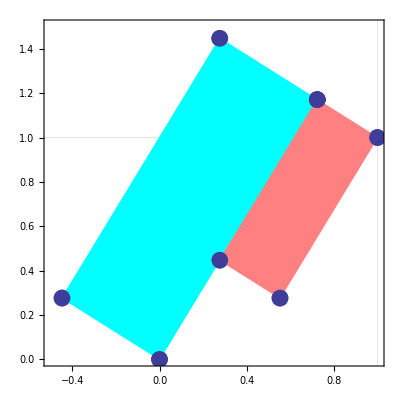

```mathematica
Show[ListPlot[Join[vertexA/.ϕDef//N,vertexB/.ϕDef//N],Frame->True, ImageSize->Scaled[0.5], PlotRange-> {{-0.5,1},{0,1.5}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{1},{1}}],
Graphics[{EdgeForm[Thick],Cyan,Polygon[vertexA/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Pink,Polygon[vertexB/.ϕDef//N]}],ListPlot[Join[vertexA/.ϕDef//N,vertexB/.ϕDef//N],Frame->True, ImageSize->Scaled[0.5], PlotRange-> {{-0.5,1},{0,1.5}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{1},{1}}]]
```

The union of A and B is another fundamental domain of the torus.

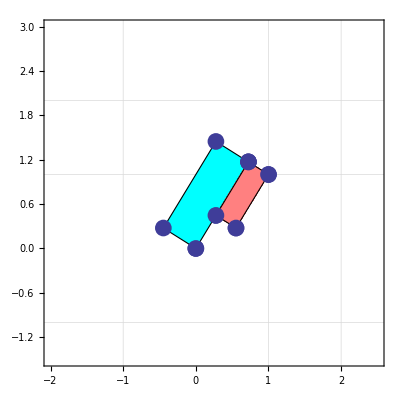

```mathematica
Flatten[Table[g[{i,j},#]&/@vertexA/.ϕDef//N,{i,-2,2},{j,-2,2}],1];
Atiling = Graphics[{EdgeForm[{Thick,Gray}],Transparent,Polygon[#]}]&/@%;
Flatten[Table[g[{i,j},#]&/@vertexB/.ϕDef//N,{i,-2,2},{j,-2,2}],1];
Btiling = Graphics[{EdgeForm[{Thick,Gray}],Transparent,Polygon[#]}]&/@%;
Show[ListPlot[Join[vertexA,vertexB/.ϕDef//N],Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-2,2.5},{-1.5,3}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{-1,1,2},{-1,1,2}}],
Graphics[{EdgeForm[{Thick,Black}],Cyan,Polygon[vertexA/.ϕDef//N]}],Graphics[{EdgeForm[{Thick,Black}],Pink,Polygon[vertexB/.ϕDef//N]}],Atiling,Btiling,ListPlot[Join[vertexA/.ϕDef//N,vertexB/.ϕDef//N],Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-2,2.5},{-1.5,3}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{-1,1,2},{-1,1,2}}]]
```

The intersection of the images of A and B with A and B under the half map.

```mathematica
vertexAimage = half𝔉/@vertexA
%/.ϕDef//Simplify
%//N
```

{{0,0},{1/(1+ϕ^2),1/(1+ϕ^2)-ϕ/(1+ϕ^2)},{(1+ϕ+ϕ^2)/(1+ϕ^2),1/(1+ϕ^2)+(1+ϕ+ϕ^2)/(1+ϕ^2)},{(ϕ (1+ϕ))/(1+ϕ^2),(1+ϕ)/(1+ϕ^2)+(ϕ (1+ϕ))/(1+ϕ^2)}}

{{0,0},{1/10 (5-√5),1/10 (5-3 √5)},{1+1/(√5),1/10 (15+√5)},{1/10 (5+3 √5),1+2/(√5)}}

{{0.,0.},{0.276393,-0.17082},{1.44721,1.72361},{1.17082,1.89443}}

```mathematica
vertexBimage = half𝔉/@vertexB
%/.ϕDef//Simplify
%//N
```

{{ϕ/(1+ϕ^2),1/(1+ϕ^2)+ϕ/(1+ϕ^2)},{(ϕ (1+ϕ))/(1+ϕ^2),(1+ϕ)/(1+ϕ^2)+(ϕ (1+ϕ))/(1+ϕ^2)},{1,2},{1/(1+ϕ^2),1/(1+ϕ^2)+(1-ϕ+ϕ^2)/(1+ϕ^2)}}

{{1/(√5),1/10 (5+√5)},{1/10 (5+3 √5),1+2/(√5)},{1,2},{1/10 (5-√5),-3/10 (-5+√5)}}

{{0.447214,0.723607},{1.17082,1.89443},{1.,2.},{0.276393,0.82918}}

```mathematica
vertexAg[1,1] = g[{1,1},#]&/@vertexA
%/.ϕDef//Simplify
%//N
vertexAg[0,-1] = g[{0,-1},#]&/@vertexA
%/.ϕDef//Simplify
%//N
```

{{1,1},{1-ϕ/(1+ϕ^2),1+1/(1+ϕ^2)},{1+1/(1+ϕ^2),1+(1+ϕ+ϕ^2)/(1+ϕ^2)},{1+(1+ϕ)/(1+ϕ^2),1+(ϕ (1+ϕ))/(1+ϕ^2)}}

{{1,1},{1-1/(√5),3/2-1/(2 √5)},{3/2-1/(2 √5),2+1/(√5)},{1/10 (15+√5),3/10 (5+√5)}}

{{1.,1.},{0.552786,1.27639},{1.27639,2.44721},{1.72361,2.17082}}

{{0,-1},{-ϕ/(1+ϕ^2),-1+1/(1+ϕ^2)},{1/(1+ϕ^2),-1+(1+ϕ+ϕ^2)/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),-1+(ϕ (1+ϕ))/(1+ϕ^2)}}

{{0,-1},{-1/(√5),1/10 (-5-√5)},{1/10 (5-√5),1/(√5)},{1/10 (5+√5),1/10 (-5+3 √5)}}

{{0.,-1.},{-0.447214,-0.723607},{0.276393,0.447214},{0.723607,0.17082}}

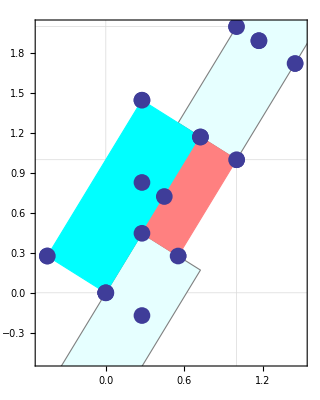

```mathematica
Show[ListPlot[Join[vertexA/.ϕDef//N,vertexB/.ϕDef//N,vertexAimage/.ϕDef//N,vertexBimage/.ϕDef//N],Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-0.5,1.5},{-0.5,2}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{0,1,2,3},{0,1,2,3}}],
Graphics[{EdgeForm[{Thick,Gray}],LightCyan,Polygon[vertexAg[1,1]/.ϕDef//N]}],Graphics[{EdgeForm[{Thick,Gray}],LightCyan,Polygon[vertexAg[0,-1]/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Cyan,Polygon[vertexA/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Pink,Polygon[vertexB]/.ϕDef//N}],Graphics[{EdgeForm[Thick],Transparent,Polygon[vertexAimage/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Transparent,Polygon[vertexBimage/.ϕDef//N]}],
ListPlot[Join[vertexA/.ϕDef//N,vertexB/.ϕDef//N,vertexAimage/.ϕDef//N,vertexBimage/.ϕDef//N],Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-0.5,1.5},{-0.5,2}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{0,1,2,3},{0,1,2,3}}]]
```

The intersection of halfF(A) and A is made of 2 disconnected components.
The intersection of halfF(A) and B is made of 1 component.
The intersection of halfF(B) and A is made of 2 disconnected components.
The intersection of halfF(B) and B is made of 0 components.

The intersection of the images of A and B with A and B under the cat map.

```mathematica
vertexAimage = 𝔉/@vertexA
%/.ϕDef//Simplify
%//N
```

{{0,0},{1/(1+ϕ^2)-ϕ/(1+ϕ^2),2/(1+ϕ^2)-ϕ/(1+ϕ^2)},{1/(1+ϕ^2)+(1+ϕ+ϕ^2)/(1+ϕ^2),1/(1+ϕ^2)+(2 (1+ϕ+ϕ^2))/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2)+(ϕ (1+ϕ))/(1+ϕ^2),(1+ϕ)/(1+ϕ^2)+(2 ϕ (1+ϕ))/(1+ϕ^2)}}

{{0,0},{1/10 (5-3 √5),1-2/(√5)},{1/10 (15+√5),5/2+3/(2 √5)},{1+2/(√5),3/2+7/(2 √5)}}

{{0.,0.},{-0.17082,0.105573},{1.72361,3.17082},{1.89443,3.06525}}

```mathematica
vertexBimage = 𝔉/@vertexB
%/.ϕDef//Simplify
%//N
```

{{1/(1+ϕ^2)+ϕ/(1+ϕ^2),1/(1+ϕ^2)+(2 ϕ)/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2)+(ϕ (1+ϕ))/(1+ϕ^2),(1+ϕ)/(1+ϕ^2)+(2 ϕ (1+ϕ))/(1+ϕ^2)},{2,3},{1/(1+ϕ^2)+(1-ϕ+ϕ^2)/(1+ϕ^2),2/(1+ϕ^2)+(1-ϕ+ϕ^2)/(1+ϕ^2)}}

{{1/10 (5+√5),1/10 (5+3 √5)},{1+2/(√5),3/2+7/(2 √5)},{2,3},{-3/10 (-5+√5),2-2/(√5)}}

{{0.723607,1.17082},{1.89443,3.06525},{2.,3.},{0.82918,1.10557}}

```mathematica
vertexAg[1,1] = g[{1,1},#]&/@vertexA
%/.ϕDef//Simplify
%//N
vertexBg[1,2] = g[{1,2},#]&/@vertexB
%/.ϕDef//Simplify
%//N
```

{{1,1},{1-ϕ/(1+ϕ^2),1+1/(1+ϕ^2)},{1+1/(1+ϕ^2),1+(1+ϕ+ϕ^2)/(1+ϕ^2)},{1+(1+ϕ)/(1+ϕ^2),1+(ϕ (1+ϕ))/(1+ϕ^2)}}

{{1,1},{1-1/(√5),3/2-1/(2 √5)},{3/2-1/(2 √5),2+1/(√5)},{1/10 (15+√5),3/10 (5+√5)}}

{{1.,1.},{0.552786,1.27639},{1.27639,2.44721},{1.72361,2.17082}}

{{1+1/(1+ϕ^2),2+ϕ/(1+ϕ^2)},{1+(1+ϕ)/(1+ϕ^2),2+(ϕ (1+ϕ))/(1+ϕ^2)},{2,3},{1+(1-ϕ+ϕ^2)/(1+ϕ^2),2+1/(1+ϕ^2)}}

{{3/2-1/(2 √5),2+1/(√5)},{1/10 (15+√5),5/2+3/(2 √5)},{2,3},{2-1/(√5),5/2-1/(2 √5)}}

{{1.27639,2.44721},{1.72361,3.17082},{2.,3.},{1.55279,2.27639}}

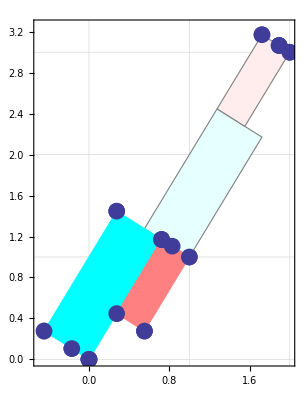

```mathematica
Show[ListPlot[Join[vertexA/.ϕDef//N,vertexB/.ϕDef//N,vertexAimage/.ϕDef//N,vertexBimage]/.ϕDef//N,Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-0.5,2},{0,3.25}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{0,1,2,3},{0,1,2,3}}],
Graphics[{EdgeForm[{Thick,Gray}],LightCyan,Polygon[vertexAg[1,1]/.ϕDef//N]}],Graphics[{EdgeForm[{Thick,Gray}],LightPink,Polygon[vertexBg[1,2]/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Cyan,Polygon[vertexA/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Pink,Polygon[vertexB/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Transparent,Polygon[vertexAimage/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Transparent,Polygon[vertexBimage/.ϕDef//N]}],
ListPlot[Join[vertexA/.ϕDef//N,vertexB/.ϕDef//N,vertexAimage/.ϕDef//N,vertexBimage/.ϕDef//N],Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-0.5,2},{0,3.25}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{0,1,2,3},{0,1,2,3}}]]
```

The intersection of F(A) and A is made of 2 disconnected component.
The intersection of F(A) and B is made of 1 component.
The intersection of F(B) and A is made of 1 component.
The intersection of F(B) and B is made of 1 component.

The intersection of the images of A and B with A and B under the inverse cat map.

```mathematica
vertexApreimage = inv𝔉/@vertexA
%/.ϕDef//Simplify
%//N
```

{{0,0},{-1/(1+ϕ^2)-(2 ϕ)/(1+ϕ^2),1/(1+ϕ^2)+ϕ/(1+ϕ^2)},{2/(1+ϕ^2)-(1+ϕ+ϕ^2)/(1+ϕ^2),-1/(1+ϕ^2)+(1+ϕ+ϕ^2)/(1+ϕ^2)},{(2 (1+ϕ))/(1+ϕ^2)-(ϕ (1+ϕ))/(1+ϕ^2),-(1+ϕ)/(1+ϕ^2)+(ϕ (1+ϕ))/(1+ϕ^2)}}

{{0,0},{1/10 (-5-3 √5),1/10 (5+√5)},{-2/(√5),1/10 (5+3 √5)},{1/10 (5-√5),1/(√5)}}

{{0.,0.},{-1.17082,0.723607},{-0.894427,1.17082},{0.276393,0.447214}}

```mathematica
vertexBpreimage = inv𝔉/@vertexB
%/.ϕDef//Simplify
%//N
```

{{2/(1+ϕ^2)-ϕ/(1+ϕ^2),-1/(1+ϕ^2)+ϕ/(1+ϕ^2)},{(2 (1+ϕ))/(1+ϕ^2)-(ϕ (1+ϕ))/(1+ϕ^2),-(1+ϕ)/(1+ϕ^2)+(ϕ (1+ϕ))/(1+ϕ^2)},{1,0},{-1/(1+ϕ^2)+(2 (1-ϕ+ϕ^2))/(1+ϕ^2),1/(1+ϕ^2)-(1-ϕ+ϕ^2)/(1+ϕ^2)}}

{{1-2/(√5),1/10 (-5+3 √5)},{1/10 (5-√5),1/(√5)},{1,0},{-3/10 (-5+√5),1/10 (-5+√5)}}

{{0.105573,0.17082},{0.276393,0.447214},{1.,0.},{0.82918,-0.276393}}

```mathematica
vertexAg[-1,0] = g[{-1,0},#]&/@vertexA
%/.ϕDef//Simplify
%//N
```

{{-1,0},{-1-ϕ/(1+ϕ^2),1/(1+ϕ^2)},{-1+1/(1+ϕ^2),(1+ϕ+ϕ^2)/(1+ϕ^2)},{-1+(1+ϕ)/(1+ϕ^2),(ϕ (1+ϕ))/(1+ϕ^2)}}

{{-1,0},{-1-1/(√5),1/10 (5-√5)},{1/10 (-5-√5),1+1/(√5)},{1/10 (-5+√5),1/10 (5+3 √5)}}

{{-1.,0.},{-1.44721,0.276393},{-0.723607,1.44721},{-0.276393,1.17082}}

```mathematica
vertexBg[-1,0] = g[{-1,0},#]&/@vertexB
%/.ϕDef//Simplify
%//N
```

{{-1+1/(1+ϕ^2),ϕ/(1+ϕ^2)},{-1+(1+ϕ)/(1+ϕ^2),(ϕ (1+ϕ))/(1+ϕ^2)},{0,1},{-1+(1-ϕ+ϕ^2)/(1+ϕ^2),1/(1+ϕ^2)}}

{{1/10 (-5-√5),1/(√5)},{1/10 (-5+√5),1/10 (5+3 √5)},{0,1},{-1/(√5),1/10 (5-√5)}}

{{-0.723607,0.447214},{-0.276393,1.17082},{0.,1.},{-0.447214,0.276393}}

```mathematica
vertexAg[0,-1] = g[{0,-1},#]&/@vertexA
%/.ϕDef//Simplify
%//N
```

{{0,-1},{-ϕ/(1+ϕ^2),-1+1/(1+ϕ^2)},{1/(1+ϕ^2),-1+(1+ϕ+ϕ^2)/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),-1+(ϕ (1+ϕ))/(1+ϕ^2)}}

{{0,-1},{-1/(√5),1/10 (-5-√5)},{1/10 (5-√5),1/(√5)},{1/10 (5+√5),1/10 (-5+3 √5)}}

{{0.,-1.},{-0.447214,-0.723607},{0.276393,0.447214},{0.723607,0.17082}}

```mathematica
vertexBg[0,-1] = g[{0,-1},#]&/@vertexB
%/.ϕDef//Simplify
%//N
```

{{1/(1+ϕ^2),-1+ϕ/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),-1+(ϕ (1+ϕ))/(1+ϕ^2)},{1,0},{(1-ϕ+ϕ^2)/(1+ϕ^2),-1+1/(1+ϕ^2)}}

{{1/10 (5-√5),-1+1/(√5)},{1/10 (5+√5),1/10 (-5+3 √5)},{1,0},{1-1/(√5),1/10 (-5-√5)}}

{{0.276393,-0.552786},{0.723607,0.17082},{1.,0.},{0.552786,-0.723607}}

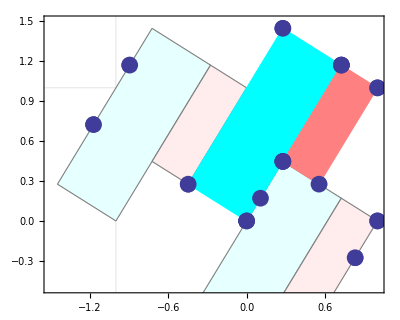

```mathematica
Show[ListPlot[Join[vertexA/.ϕDef//N,vertexB/.ϕDef//N,vertexApreimage/.ϕDef//N,vertexBpreimage]/.ϕDef//N,Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-1.5,1},{-0.5,1.5}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{-1},{1}}],
Graphics[{EdgeForm[{Thick,Gray}],LightCyan,Polygon[vertexAg[-1,0]/.ϕDef//N]}],Graphics[{EdgeForm[{Thick,Gray}],LightPink,Polygon[vertexBg[-1,0]/.ϕDef//N]}],Graphics[{EdgeForm[{Thick,Gray}],LightCyan,Polygon[vertexAg[0,-1]/.ϕDef//N]}],Graphics[{EdgeForm[{Thick,Gray}],LightPink,Polygon[vertexBg[0,-1]/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Cyan,Polygon[vertexA/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Pink,Polygon[vertexB/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Transparent,Polygon[vertexApreimage/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Transparent,Polygon[vertexBpreimage/.ϕDef//N]}],
ListPlot[Join[vertexA/.ϕDef//N,vertexB/.ϕDef//N,vertexApreimage/.ϕDef//N,vertexBpreimage]/.ϕDef//N,Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-1.5,1},{-0.5,1.5}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{-1},{1}}]]
```

The intersection of F^-1(A) and A is made of 2 disconnected components.
The intersection of F^-1(A) and B is made of 1 component.
The intersection of F^-1(B) and A is made of 1 component.
The intersection of F^-1(B) and B is made of 1 component.

An important point to make is that any density distribution on the cover space ℝ^2 with wave vectors commensurate to the fundamental domain [0,1[^2 (that is with integer wave numbers) is also a density distribution on the torus 𝕋^2. Replacing the fundamental domain [0,1[^2 with A∩B does not change that. This is because these distributions are invariant under the action of the fundamental group.

```mathematica
{kx,ky}={1,1}
Show[DensityPlot[Sin[2 Pi {kx,ky}.{x,y}]^2, {x,-2,2.5},{y,-2,3},Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-2,2.5},{-1.5,3}}, AspectRatio->Automatic,GridLines -> {{-1,1,2},{-1,1,2}},ColorFunction->"SunsetColors",MaxRecursion->4],
Atiling,Btiling]
```

{1,1}

-Graphics-

On the other hand density distributions with wave numbers incommensurate to [0,1[^2 are no longer defined as a simple branch on the torus. On the torus they are forms with infinitely many branches because they are not invariant under the action of the fundamental group. This is true also for distributions with wave vectors parallels to the unstable and stable manifolds of the map. This has an important consequence. If we rotate to a system of coordinates in the cover space that are parallel to the eigenvectors of the map a distribution that is a function of only one of these coordinates will not have a single branch on the torus.

{0.618034,1.}

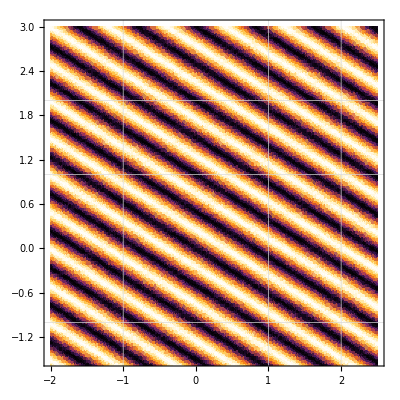

```mathematica
{kx,ky}={1/ϕ,1}/.ϕDef//N
Show[DensityPlot[Sin[2 Pi {kx,ky}.{x,y}]^2, {x,-2,2.5},{y,-2,3},Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-2,2.5},{-1.5,3}}, AspectRatio->Automatic,GridLines -> {{-1,1,2},{-1,1,2}},ColorFunction->"SunsetColors",MaxRecursion->4],
Atiling,Btiling]
```

```mathematica
{kx,ky}={-ϕ,1}/.ϕDef//N
Show[DensityPlot[Sin[2 Pi {kx,ky}.{x,y}]^2, {x,-2,2.5},{y,-2,3},Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-2,2.5},{-1.5,3}}, AspectRatio->Automatic,GridLines -> {{-1,1,2},{-1,1,2}},ColorFunction->"SunsetColors",MaxRecursion->5],
Atiling,Btiling]
```

{-1.61803,1.}

-Graphics-

### Five-Cell Partition

Construction of the cells of the Markov partition using the intersections of the images of A and B with A and B.

```mathematica
vertexD = Table[{},{i,5}];
```

```mathematica
vertexD[[1]] = {vertexA[[2]],vertexA[[3]]};
Solve[sm[-2,2,x]== um[0,0,x],x]
vertexD[[1]] = Append[vertexD[[1]],g[{-1,-1},#]&@{x/.%[[1]],um[0,0,x]/.%[[1]]}];
vertexD[[1]] = Simplify@Append[vertexD[[1]],g[{-1,-1},#]&@vertexA[[4]]]
%/.ϕDef//Simplify
%//N
```

{{x→(2 (1+ϕ))/(1+ϕ^2)}}

{{-ϕ/(1+ϕ^2),1/(1+ϕ^2)},{1/(1+ϕ^2),(1+ϕ+ϕ^2)/(1+ϕ^2)},{-1+(2 (1+ϕ))/(1+ϕ^2),-1+(2 ϕ (1+ϕ))/(1+ϕ^2)},{-1+(1+ϕ)/(1+ϕ^2),(-1+ϕ)/(1+ϕ^2)}}

{{-1/(√5),1/10 (5-√5)},{1/10 (5-√5),1+1/(√5)},{1/(√5),3/(√5)},{1/10 (-5+√5),1/10 (-5+3 √5)}}

{{-0.447214,0.276393},{0.276393,1.44721},{0.447214,1.34164},{-0.276393,0.17082}}

```mathematica
vertexD[[2]] = {vertexD[[1,4]],vertexD[[1,3]]};
Solve[sm[-2,2,x]== um[-2,3,x],x]
vertexD[[2]] = Append[vertexD[[2]],g[{-1,-1},#]&@{x/.%[[1]],um[-2,3,x]/.%[[1]]}];
vertexD[[2]] = Simplify@Append[vertexD[[2]],vertexAimage[[2]]]
%/.ϕDef//Simplify
%//N
```

{{x→(2-ϕ+2 ϕ^2)/(1+ϕ^2)}}

{{-1+(1+ϕ)/(1+ϕ^2),(-1+ϕ)/(1+ϕ^2)},{-1+(2 (1+ϕ))/(1+ϕ^2),-1+(2 ϕ (1+ϕ))/(1+ϕ^2)},{(1-ϕ+ϕ^2)/(1+ϕ^2),(2+ϕ^2)/(1+ϕ^2)},{(1-ϕ)/(1+ϕ^2),(2-ϕ)/(1+ϕ^2)}}

{{1/10 (-5+√5),1/10 (-5+3 √5)},{1/(√5),3/(√5)},{1-1/(√5),3/2-1/(2 √5)},{1/10 (5-3 √5),1-2/(√5)}}

{{-0.276393,0.17082},{0.447214,1.34164},{0.552786,1.27639},{-0.17082,0.105573}}

```mathematica
vertexD[[3]] = {vertexD[[2,4]],vertexD[[2,3]],vertexA[[4]],vertexA[[1]]}
%/.ϕDef//Simplify
%//N
```

{{(1-ϕ)/(1+ϕ^2),(2-ϕ)/(1+ϕ^2)},{(1-ϕ+ϕ^2)/(1+ϕ^2),(2+ϕ^2)/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),(ϕ (1+ϕ))/(1+ϕ^2)},{0,0}}

{{1/10 (5-3 √5),1-2/(√5)},{1-1/(√5),3/2-1/(2 √5)},{1/10 (5+√5),1/10 (5+3 √5)},{0,0}}

{{-0.17082,0.105573},{0.552786,1.27639},{0.723607,1.17082},{0.,0.}}

```mathematica
vertexD[[4]] = {vertexB[[1]],vertexB[[2]]}
Solve[sm[-2,3,x]== um[0,0,x],x]
vertexD[[4]] = Append[vertexD[[4]],g[{-1,-2},#]&@{x/.%[[1]],um[0,0,x]/.%[[1]]}];
Solve[sm[-2,2,x]== um[0,0,x],x]
vertexD[[4]]= Simplify@Append[vertexD[[4]],g[{-1,-2},#]&@{x/.%[[1]],um[0,0,x]/.%[[1]]}];
%/.ϕDef//Simplify
%//N
```

{{1/(1+ϕ^2),ϕ/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),(ϕ (1+ϕ))/(1+ϕ^2)}}

{{x→(2+3 ϕ)/(1+ϕ^2)}}

{{x→(2 (1+ϕ))/(1+ϕ^2)}}

{{1/10 (5-√5),1/(√5)},{1/10 (5+√5),1/10 (5+3 √5)},{2/(√5),1/10 (-5+7 √5)},{1/(√5),-1+3/(√5)}}

{{0.276393,0.447214},{0.723607,1.17082},{0.894427,1.06525},{0.447214,0.341641}}

```mathematica
vertexD[[5]] = {vertexD[[4,4]],vertexD[[4,3]],vertexB[[3]],vertexB[[4]]}
%/.ϕDef//Simplify
%//N
```

{{-1+(2 (1+ϕ))/(1+ϕ^2),(2 (-1+ϕ))/(1+ϕ^2)},{-1+(2+3 ϕ)/(1+ϕ^2),(-2+2 ϕ+ϕ^2)/(1+ϕ^2)},{1,1},{(1-ϕ+ϕ^2)/(1+ϕ^2),1/(1+ϕ^2)}}

{{1/(√5),-1+3/(√5)},{2/(√5),1/10 (-5+7 √5)},{1,1},{1-1/(√5),1/10 (5-√5)}}

{{0.447214,0.341641},{0.894427,1.06525},{1.,1.},{0.552786,0.276393}}

```mathematica
vertexD
%/.ϕDef//Simplify
%//N
```

{{{-ϕ/(1+ϕ^2),1/(1+ϕ^2)},{1/(1+ϕ^2),(1+ϕ+ϕ^2)/(1+ϕ^2)},{-1+(2 (1+ϕ))/(1+ϕ^2),-1+(2 ϕ (1+ϕ))/(1+ϕ^2)},{-1+(1+ϕ)/(1+ϕ^2),(-1+ϕ)/(1+ϕ^2)}},{{-1+(1+ϕ)/(1+ϕ^2),(-1+ϕ)/(1+ϕ^2)},{-1+(2 (1+ϕ))/(1+ϕ^2),-1+(2 ϕ (1+ϕ))/(1+ϕ^2)},{(1-ϕ+ϕ^2)/(1+ϕ^2),(2+ϕ^2)/(1+ϕ^2)},{(1-ϕ)/(1+ϕ^2),(2-ϕ)/(1+ϕ^2)}},{{(1-ϕ)/(1+ϕ^2),(2-ϕ)/(1+ϕ^2)},{(1-ϕ+ϕ^2)/(1+ϕ^2),(2+ϕ^2)/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),(ϕ (1+ϕ))/(1+ϕ^2)},{0,0}},{{1/(1+ϕ^2),ϕ/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),(ϕ (1+ϕ))/(1+ϕ^2)},{-1+(2+3 ϕ)/(1+ϕ^2),(-2+2 ϕ+ϕ^2)/(1+ϕ^2)},{-1+(2 (1+ϕ))/(1+ϕ^2),(2 (-1+ϕ))/(1+ϕ^2)}},{{-1+(2 (1+ϕ))/(1+ϕ^2),(2 (-1+ϕ))/(1+ϕ^2)},{-1+(2+3 ϕ)/(1+ϕ^2),(-2+2 ϕ+ϕ^2)/(1+ϕ^2)},{1,1},{(1-ϕ+ϕ^2)/(1+ϕ^2),1/(1+ϕ^2)}}}

{{{-1/(√5),1/10 (5-√5)},{1/10 (5-√5),1+1/(√5)},{1/(√5),3/(√5)},{1/10 (-5+√5),1/10 (-5+3 √5)}},{{1/10 (-5+√5),1/10 (-5+3 √5)},{1/(√5),3/(√5)},{1-1/(√5),3/2-1/(2 √5)},{1/10 (5-3 √5),1-2/(√5)}},{{1/10 (5-3 √5),1-2/(√5)},{1-1/(√5),3/2-1/(2 √5)},{1/10 (5+√5),1/10 (5+3 √5)},{0,0}},{{1/10 (5-√5),1/(√5)},{1/10 (5+√5),1/10 (5+3 √5)},{2/(√5),1/10 (-5+7 √5)},{1/(√5),-1+3/(√5)}},{{1/(√5),-1+3/(√5)},{2/(√5),1/10 (-5+7 √5)},{1,1},{1-1/(√5),1/10 (5-√5)}}}

{{{-0.447214,0.276393},{0.276393,1.44721},{0.447214,1.34164},{-0.276393,0.17082}},{{-0.276393,0.17082},{0.447214,1.34164},{0.552786,1.27639},{-0.17082,0.105573}},{{-0.17082,0.105573},{0.552786,1.27639},{0.723607,1.17082},{0.,0.}},{{0.276393,0.447214},{0.723607,1.17082},{0.894427,1.06525},{0.447214,0.341641}},{{0.447214,0.341641},{0.894427,1.06525},{1.,1.},{0.552786,0.276393}}}

```mathematica
vertices = Flatten[vertexD,1];
```

```mathematica
partition[0,0] = {Graphics[{EdgeForm[Thick],Blue,Polygon[vertexD[[1]]]}],Graphics[{EdgeForm[Thick],Purple,Polygon[vertexD[[2]]]}],Graphics[{EdgeForm[Thick],Blue,Polygon[vertexD[[3]]]}],Graphics[{EdgeForm[Thick],Purple,Polygon[vertexD[[4]]]}],Graphics[{EdgeForm[Thick],Red,Polygon[vertexD[[5]]]}]};
```

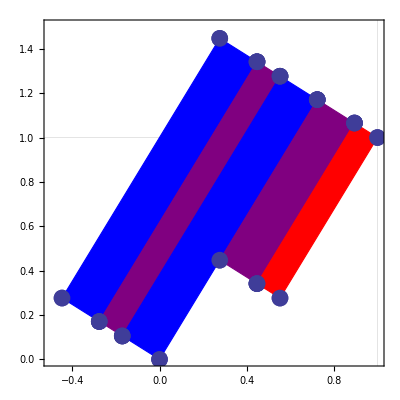

```mathematica
Show[ListPlot[vertices/.ϕDef//N,Frame->True, ImageSize->Scaled[0.5], PlotRange-> {{-0.5,1},{0,1.5}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{1},{1}}],
Graphics[{EdgeForm[Thick],Transparent,Polygon[vertexA/.ϕDef//N]}],Graphics[{EdgeForm[Thick],Transparent,Polygon[vertexB/.ϕDef//N]}],
partition[0,0]/.ϕDef//N,ListPlot[vertices/.ϕDef//N,Frame->True, ImageSize->Full, PlotRange-> {{-0.5,1},{0,1.5}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{1},{1}}]]
```

The intersections of the images of the cells with the original cells in the universal covering space.

```mathematica
imageOfVertexD[0,0] = Map[𝔉,vertexD,{2}];
vertexDg[1,1] = Map[g[{1,1},#]&,vertexD,{2}];
partition[1,1] = Graphics[{EdgeForm[{Thick,Gray}],Transparent,Polygon[#]}]&/@vertexDg[1,1];
imageOfPartition[0,0] = Graphics[{EdgeForm[Thick],Transparent,Polygon[#]}]&/@imageOfVertexD[0,0];
```

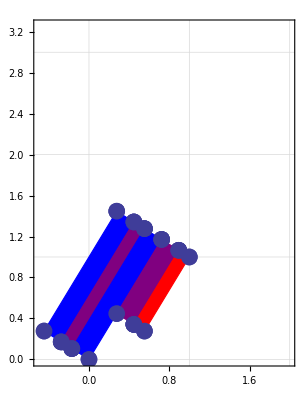

```mathematica
Show[ListPlot[vertices/.ϕDef//N,Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-0.5,2},{0,3.25}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{0,1,2,3},{0,1,2,3}}],
partition[1,1]/.ϕDef//N,
partition[0,0]/.ϕDef//N,
imageOfPartition[0,0]/.ϕDef//N,
ListPlot[vertices/.ϕDef//N,Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{-0.5,2},{0,3.25}}, PlotStyle->PointSize[0.03], AspectRatio->Automatic,GridLines -> {{0,1,2,3},{0,1,2,3}}]]
```

All intersections between F(D_i) and D_j are simply connected.

### Adjacency Matrix and Grammar

The adjacency matrix of the Markov partition.

```mathematica
intersection[i_Integer,j_Integer] := 0
intersection[1,3]:=1
intersection[1,1]:=1
intersection[1,4]:=1
intersection[2,3]:=1
intersection[2,1]:=1
intersection[2,4]:=1
intersection[3,3]:=1
intersection[3,1]:=1
intersection[3,4]:=1
intersection[4,2]:=1
intersection[4,5]:=1
intersection[5,2]:=1
intersection[5,5]:=1
```

```mathematica
adjacencyMatrix := Table[intersection[i,j],{i,1,5},{j,1,5}]
```

```mathematica
TraditionalForm[adjacencyMatrix]
```

(1 | 0 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1)

```mathematica
Eigenvalues[adjacencyMatrix]
```

{1/2 (3+√5),1/2 (3-√5),0,0,0}

```mathematica
Eigenvectors[adjacencyMatrix]
```

{{1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1,1},{1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1,1},{0,-1,0,0,1},{-1,0,0,1,0},{-1,0,1,0,0}}

The grammar of the symbolic dynamics.

```mathematica
AdjacencyGraph[adjacencyMatrix,GraphStyle->"VintageDiagram"]
```

-Graphics-

### Zeta Function

```mathematica
Det[IdentityMatrix[5]-z adjacencyMatrix]
```

1-3 z+z^2

```mathematica
zeta[z_] := 1/Det[IdentityMatrix[5]-z adjacencyMatrix]
```

```mathematica
Roots[1/zeta[z] == 0 , z]
```

z==1/2 (3-√5)||z==1/2 (3+√5)

```mathematica
Plot3D[Abs[zeta[x+I y]],{x,-1,4},{y,-2,2},AspectRatio->Automatic,ImageSize->Scaled[0.5],PlotRange->{0,5}]
```

-Graphics3D-

### Iterating the Partition

The Markov partition and the first iterate of it in the fundamental domain.

```mathematica
vertexDg[0,-1] = Map[g[{0,-1},#]&,vertexD,{2}];
vertexDg[1,0] = Map[g[{1,0},#]&,vertexD,{2}];
preimageOfVertexD[0,0] = Map[inv𝔉,vertexD,{2}];
preimageOfVertexD[1,0]= Map[g[{1,0},#]&,preimageOfVertexD[0,0],{2}];
preimageOfVertexD[0,1]= Map[g[{0,1},#]&,preimageOfVertexD[0,0],{2}];
```

```mathematica
partition[0,0] = Graphics[{EdgeForm[{Thick}],Transparent,Polygon[#]}]&/@vertexD;
partition[0,-1] = Graphics[{EdgeForm[{Thick}],Transparent,Polygon[#]}]&/@vertexDg[0,-1] ; partition[1,0] = Graphics[{EdgeForm[{Thick}],Transparent,Polygon[#]}]&/@vertexDg[1,0] ;
preImageOfPartition[0,0] = Graphics[{EdgeForm[{Thick}],Transparent,Polygon[#]}]&/@preimageOfVertexD[0,0]; 
preImageOfPartition[1,0] = Graphics[{EdgeForm[{Thick}],Transparent,Polygon[#]}]&/@preimageOfVertexD[1,0]; 
preImageOfPartition[0,1] = Graphics[{EdgeForm[{Thick}],Transparent,Polygon[#]}]&/@preimageOfVertexD[0,1];
```

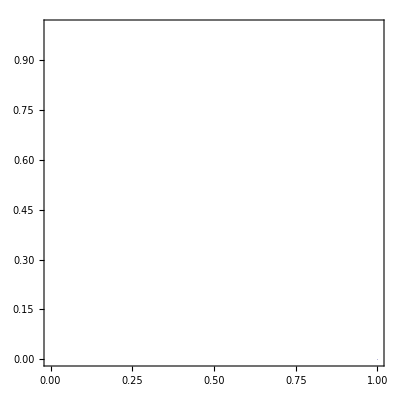

```mathematica
Show[
ListPlot[{0,0},Frame->True, ImageSize->Scaled[0.5], PlotRange-> {{0,1},{0,1}}, PlotStyle->PointSize[0], AspectRatio->Automatic],
partition[0,0]/.ϕDef//N,partition[0,-1]/.ϕDef//N,partition[1,0]/.ϕDef//N,preImageOfPartition[1,0]/.ϕDef//N,
preImageOfPartition[0,0]/.ϕDef//N,preImageOfPartition[0,1]/.ϕDef//N
]
```

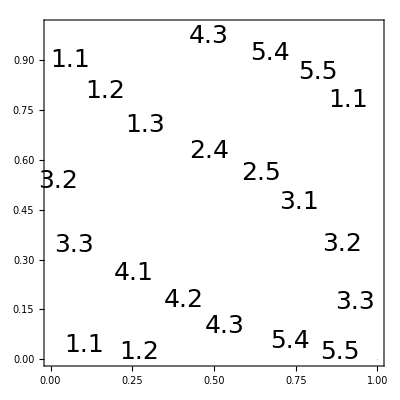

### Symbolic Dynamics

The crossings of the stable and unstable manifold with the border of the fundamental domain.

```mathematica
y0um[1,-1]==1/ϕ
%/.ϕDef
```

-1+ϕ==1/ϕ

True

```mathematica
y0um[-1,2]==1/(ϕ+1)
%/.ϕDef
```

2-ϕ==1/(1+ϕ)

True

```mathematica
x1um[1,-2]==(1+ϕ^2)/(ϕ+ϕ^2)
%/.ϕDef
```

-1+3/ϕ==(1+ϕ^2)/(ϕ+ϕ^2)

True

```mathematica
x1um[-1,1]==1
```

True

```mathematica
x0um[0,-1]==1/ϕ
```

True

```mathematica
y1um[-2,2]==1/(ϕ+1)
%/.ϕDef
```

2-ϕ==1/(1+ϕ)

True

```mathematica
x0um[1,-3] == (1+ϕ^2)/(ϕ+ϕ^2)
%/.ϕDef
```

-1+3/ϕ==(1+ϕ^2)/(ϕ+ϕ^2)

True

```mathematica
y1sm[-2,0]==1/ϕ
```

True

```mathematica
y0sm[-1,0]==1/ϕ
```

True

```mathematica
x0sm[-2,-1]==1/(ϕ+1)
%/.ϕDef
```

2-ϕ==1/(1+ϕ)

True

The cells of the Markov partition in the fundamental domain.

```mathematica
isInD[1,{x_,y_}]:= (sm[-1,0,x] < y && um[0,-1,x] < y && y<um[-1,1,x]) ||
(um[1,-1,x] < y) || (um[1,-2,x] < y && y<um[0,0,x]  && y < sm[-1,0,x])
isInD[2,{x_,y_}]:= (sm[-1,0,x] < y && um[-2,2,x] < y&&  y< um[0,-1,x]) || (um[-1,2,x]< y &&  y< um[1,-1,x]) || (um[-1,1,x] < y  &&  y< um[1,-2,x] && y<sm[-1,0,x] )
isInD[3,{x_,y_}] := (sm[-1,0,x] < y  && y < um[-2,2,x]) || (um[0,0,x] < y && y < um[-1,2,x]) || (y> um[0,-1,x] && y< um[-1,1,x] && y<sm[-1,0,x] )
isInD[4,{x_,y_}]:= (sm[-1,0,x]<y &&  um[1,-2,x] < y && y <um[0,0,x])  || (um[1,-3,x]<y&& y<sm[-1,0,x] && y< um[0,-1,x] )
isInD[5,{x_,y_}]:= (sm[-1,0,x] <y &&  um[-1,1,x] < y && y<um[1,-2,x]) || (y<um[1,-3,x] && y< sm[-1,0,x] )
```

```mathematica
testInD[11,{x_,y_}] :=sm[-1,0,x]<y
testInD[12,{x_,y_}] := um[1,-2,x] < y
testInD[13,{x_,y_}] := y <um[0,0,x]
testInD[1,{x_,y_}] := testInD[11,{x,y}]&& testInD[12,{x,y}]&& testInD[13,{x,y}]
testInD[21,{x_,y_}] :=um[1,-3,x]<y
testInD[22,{x_,y_}] := y<sm[-1,0,x]
testInD[23,{x_,y_}] := y< um[0,-1,x]
testInD[2,{x_,y_}] := testInD[21,{x,y}]&& testInD[22,{x,y}]&& testInD[23,{x,y}]
testInD[31,{x_,y_}] :=False
testInD[32,{x_,y_}] := False
testInD[33,{x_,y_}] := False
testInD[3,{x_,y_}] := testInD[31,{x,y}]&& testInD[32,{x,y}]&& testInD[33,{x,y}]
```

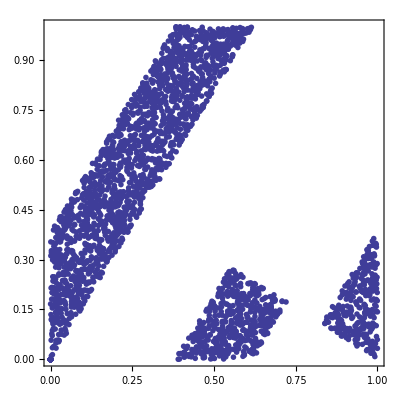

```mathematica
cellDistribution[0]=If[isInD[3,#],#,{0,0}]&/@ randomPoints/.ϕDef//N;
ListPlot[cellDistribution[0],Frame->True, ImageSize->Scaled[0.5], PlotRange-> {{0,1},{0,1}}, PlotStyle->PointSize[0.01], AspectRatio->Automatic]
```

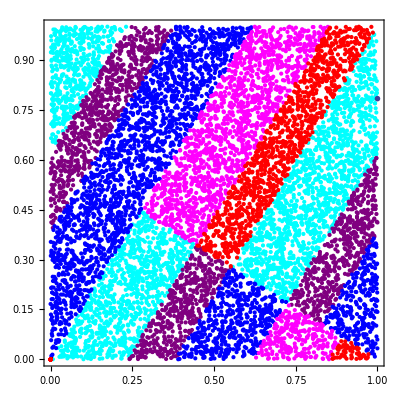

```mathematica
Do[cellDistribution[i]=If[isInD[i,#],#,{0,0}]&/@ randomPoints/.ϕDef//N,{i,5}]
cellDistributions = Table[cellDistribution[i],{i,5}];
plotOfAllCells = ListPlot[cellDistributions,Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{0,1},{0,1}}, PlotStyle->{Cyan,Purple,Blue,Magenta,Red},AspectRatio->Automatic];
plotOfOnePoint=ListPlot[{Flatten[randomPoints,1][[1]]},PlotStyle->{PointSize[0.01]}];
Show[plotOfAllCells,plotOfOnePoint]
```

The cells of the preimage of the Markov partition in the fundamental domain.

```mathematica
isInD[-1,{x_,y_}]:= (sm[-1,0,x] < y && um[0,0,x]< y && y<sm[-2,0,x]) ||(y < um[0,0,x] && y < sm[-2,-1,x]) || (sm[-2,0,x]  < y && y< um[-1,1,x] )
isInD[-2,{x_,y_}]:= y < um[0,0,x] && sm[-1,0,x] < y && um[-1,1,x] < y && y<sm[-2,0,x]
isInD[-3,{x_,y_}] := (y < sm[-1,0,x]  && um[0,0,x] < y) || (sm[-1,0,x] < y && y < um[-1,1,x] && y < sm[-2,0,x]) 
isInD[-4,{x_,y_}]:= (sm[-2,-1,x] <y &&  um[0,-1,x]< y && y <um[0,0,x] && y < sm[-1,0,x])  || (sm[-2,0,x]<y&& um[0,0,x] < y)
isInD[-5,{x_,y_}]:= (sm[-2,0,x]<y &&  y < um[0,0,x] && um[-1,1,x] < y) || (y<um[0,-1,x] && y< sm[-1,0,x])
```

```mathematica
testInD[-11,{x_,y_}] := sm[-1,0,x] < y
testInD[-12,{x_,y_}] := um[0,0,x]< y
testInD[-13,{x_,y_}] := y<sm[-2,0,x]
testInD[-1,{x_,y_}] := testInD[-11,{x,y}]&& testInD[-12,{x,y}]&& testInD[-13,{x,y}]
testInD[-21,{x_,y_}] :=y < um[0,0,x] 
testInD[-22,{x_,y_}] := y < sm[-2,-1,x]
testInD[-23,{x_,y_}] := True
testInD[-2,{x_,y_}] := testInD[-21,{x,y}]&& testInD[-22,{x,y}]&& testInD[-23,{x,y}]
testInD[-31,{x_,y_}] :=sm[-2,0,x]  < y  
testInD[-32,{x_,y_}] :=  y< um[-1,1,x]
testInD[-33,{x_,y_}] := True
testInD[-3,{x_,y_}] := testInD[-31,{x,y}]&& testInD[-32,{x,y}]&& testInD[-33,{x,y}]
```

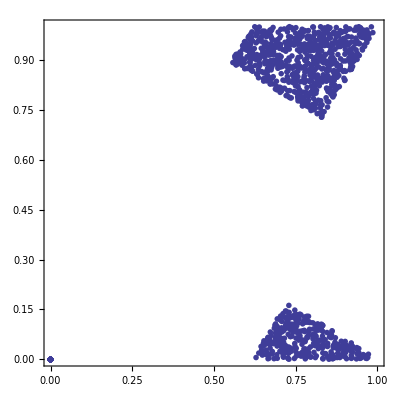

```mathematica
cellDistribution[0]=If[isInD[-5,#],#,{0,0}]&/@ randomPoints/.ϕDef//N;
ListPlot[cellDistribution[0],Frame->True, ImageSize->Scaled[0.5], PlotRange-> {{0,1},{0,1}}, PlotStyle->PointSize[0.01], AspectRatio->Automatic]
```

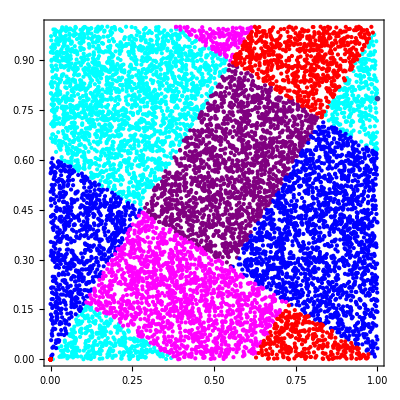

```mathematica
Do[cellDistribution[-i]=If[isInD[-i,#],#,{0,0}]&/@ randomPoints/.ϕDef//N,{i,5}]
cellDistributions = Table[cellDistribution[-i],{i,5}];
plotOfAllCells = ListPlot[cellDistributions,Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{0,1},{0,1}}, PlotStyle->{Cyan,Purple,Blue,Magenta,Red},AspectRatio->Automatic];
plotOfOnePoint=ListPlot[{Flatten[randomPoints,1][[1]]},PlotStyle->{PointSize[0.01]}];
Show[plotOfAllCells,plotOfOnePoint]
```

The symbolic dynamics

```mathematica
forwardSymbol[{x_,y_}] := Sum[If[isInD[i,{x,y}]/.ϕDef//N,i,0],{i,5}]
backwardSymbol[{x_,y_}] := Sum[If[isInD[-i,{x,y}]/.ϕDef//N,i,0],{i,5}]
```

```mathematica
Subscript[X, 0]= {RandomReal[1],RandomReal[1]}
NestList[F,Subscript[X, 0],20]
forwardSymbol/@%
NestList[invF,Subscript[X, 0],20]
Drop[%,1]
backwardSymbol/@Reverse@%
```

{0.464865,0.300961}

{{0.464865,0.300961},{0.765826,0.0667868},{0.832613,0.8994},{0.732012,0.631412},{0.363424,0.994836},{0.358261,0.353097},{0.711358,0.0644555},{0.775814,0.840269},{0.616083,0.456352},{0.0724347,0.528787},{0.601221,0.130008},{0.731229,0.861237},{0.592467,0.453704},{0.0461714,0.499876},{0.546047,0.045923},{0.59197,0.637893},{0.229864,0.867757},{0.0976203,0.965377},{0.0629975,0.0283746},{0.0913721,0.119747},{0.211119,0.330866}}

{2,4,5,5,2,1,4,5,5,2,3,4,5,2,3,4,2,1,1,1,1}

{{0.464865,0.300961},{0.628769,0.836096},{0.421443,0.207326},{0.63556,0.785883},{0.485236,0.150323},{0.820149,0.665087},{0.975211,0.844938},{0.105484,0.869727},{0.341241,0.764243},{0.918239,0.423002},{0.413476,0.504763},{0.322189,0.091287},{0.553091,0.769098},{0.337084,0.216007},{0.458161,0.878923},{0.0373982,0.420763},{0.654034,0.383364},{0.924703,0.729331},{0.120076,0.804627},{0.435524,0.684551},{0.186498,0.249027}}

{{0.628769,0.836096},{0.421443,0.207326},{0.63556,0.785883},{0.485236,0.150323},{0.820149,0.665087},{0.975211,0.844938},{0.105484,0.869727},{0.341241,0.764243},{0.918239,0.423002},{0.413476,0.504763},{0.322189,0.091287},{0.553091,0.769098},{0.337084,0.216007},{0.458161,0.878923},{0.0373982,0.420763},{0.654034,0.383364},{0.924703,0.729331},{0.120076,0.804627},{0.435524,0.684551},{0.186498,0.249027}}

{4,2,1,1,3,3,1,4,2,4,2,3,1,1,1,3,4,2,4,2}

```mathematica
Subscript[X, 0]= {0,17/22}
NestList[F,Subscript[X, 0],20]
forwardSymbol/@%
NestList[invF,Subscript[X, 0],20]
Drop[%,1]
backwardSymbol/@Reverse@%
```

{0,17/22}

{{0,17/22},{17/22,6/11},{7/22,19/22},{2/11,1/22},{5/22,3/11},{1/2,17/22},{3/11,1/22},{7/22,4/11},{15/22,1/22},{8/11,17/22},{1/2,3/11},{17/22,1/22},{9/11,19/22},{15/22,6/11},{5/22,17/22},{0,17/22},{17/22,6/11},{7/22,19/22},{2/11,1/22},{5/22,3/11},{1/2,17/22}}

{1,1,3,1,1,4,2,1,4,5,2,4,5,5,2,1,1,3,1,1,4}

{{0,17/22},{5/22,17/22},{15/22,6/11},{9/11,19/22},{17/22,1/22},{1/2,3/11},{8/11,17/22},{15/22,1/22},{7/22,4/11},{3/11,1/22},{1/2,17/22},{5/22,3/11},{2/11,1/22},{7/22,19/22},{17/22,6/11},{0,17/22},{5/22,17/22},{15/22,6/11},{9/11,19/22},{17/22,1/22},{1/2,3/11}}

{{5/22,17/22},{15/22,6/11},{9/11,19/22},{17/22,1/22},{1/2,3/11},{8/11,17/22},{15/22,1/22},{7/22,4/11},{3/11,1/22},{1/2,17/22},{5/22,3/11},{2/11,1/22},{7/22,19/22},{17/22,6/11},{0,17/22},{5/22,17/22},{15/22,6/11},{9/11,19/22},{17/22,1/22},{1/2,3/11}}

{4,5,5,2,1,1,3,1,1,4,2,1,4,5,2,4,5,5,2,1}

```mathematica
symbolicDynamics[n_Integer,{x_,y_}] := 
Join[
backwardSymbol/@ Reverse @ Drop[NestList[invF,{x,y},n],1],
{"|"},
forwardSymbol/@ NestList[F,{x,y},n]
]
```

```mathematica
Subscript[X, 0]= {RandomReal[1],RandomReal[1]}
symbolicDynamics[100,Subscript[X, 0]]
```

{0.665786,0.186502}

{2,4,2,3,4,5,2,3,3,4,2,1,4,2,3,3,3,1,4,2,4,2,3,4,5,2,3,1,1,4,5,5,5,2,3,1,3,3,1,4,2,1,1,1,4,5,5,2,1,1,1,3,3,4,2,4,5,5,2,4,2,1,1,3,3,4,5,2,3,1,3,1,3,4,2,3,1,1,3,3,1,1,1,3,3,3,3,1,3,1,1,3,1,3,1,1,3,1,3,3,|,3,4,5,5,5,2,3,3,1,1,4,2,3,3,4,5,2,3,3,4,2,4,5,2,1,1,4,2,1,4,5,2,3,4,5,2,1,1,1,3,1,3,3,3,4,5,2,1,1,3,4,5,2,1,3,1,4,2,1,1,4,2,3,1,3,4,2,1,3,1,3,4,2,3,1,1,3,1,3,3,3,3,1,1,3,3,1,4,2,1,3,4,2,1,1,4,5,2,3,4,2}

```mathematica
Subscript[X, o] = {0,17/22}
symbolicDynamics[100,Subscript[X, 0]]
```

{0,17/22}

{2,4,2,3,4,5,2,3,3,4,2,1,4,2,3,3,3,1,4,2,4,2,3,4,5,2,3,1,1,4,5,5,5,2,3,1,3,3,1,4,2,1,1,1,4,5,5,2,1,1,1,3,3,4,2,4,5,5,2,4,2,1,1,3,3,4,5,2,3,1,3,1,3,4,2,3,1,1,3,3,1,1,1,3,3,3,3,1,3,1,1,3,1,3,1,1,3,1,3,3,|,3,4,5,5,5,2,3,3,1,1,4,2,3,3,4,5,2,3,3,4,2,4,5,2,1,1,4,2,1,4,5,2,3,4,5,2,1,1,1,3,1,3,3,3,4,5,2,1,1,3,4,5,2,1,3,1,4,2,1,1,4,2,3,1,3,4,2,1,3,1,3,4,2,3,1,1,3,1,3,3,3,3,1,1,3,3,1,4,2,1,3,4,2,1,1,4,5,2,3,4,2}

### Recurrence Relation of the Partition

```mathematica
preImage2OfVertexD[0,0] = Map[inv𝔉,preimageOfVertexD[0,0],{2}];
preImage2OfPartition[0,0] = Graphics[{EdgeForm[Thin],Transparent,Polygon[#]}]&/@preImage2OfVertexD[0,0];
```

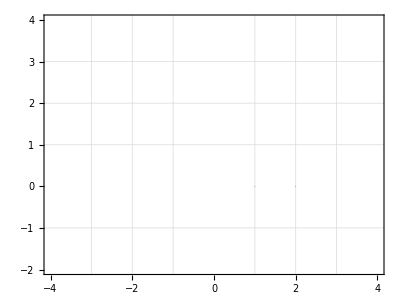

```mathematica
Show[
ListPlot[{0,0},Frame->True, ImageSize->Full, PlotRange-> {{-4,4},{-2,4}}, PlotStyle->PointSize[0], AspectRatio->Automatic, GridLines->{{-3,-2,-1,1,2,3},{-1,1,2,3}}],
partition[0,0]/.ϕDef//N,
preImageOfPartition[0,0]/.ϕDef//N,
imageOfPartition[0,0]/.ϕDef//N,
preImage2OfPartition[0,0]/.ϕDef//N
]
```

```mathematica
gg = {{0,-1},{-1,-1},{-1,-2},{-1,-3},{1,0}}
```

{{0,-1},{-1,-1},{-1,-2},{-1,-3},{1,0}}

```mathematica
Do[imageOfVertexD[gg[[i,1]],gg[[i,2]]] = Map[g[gg[[i]],#]&,imageOfVertexD[0,0],{2}], {i,Length[gg]}]
```

```mathematica
Do[ imageOfPartition[gg[[i,1]],gg[[i,2]]] = Graphics[{EdgeForm[Thin],Transparent,Polygon[#]}]&/@imageOfVertexD[gg[[i,1]],gg[[i,2]]],{i,Length[gg]}]
```

```mathematica
gg={{1,0},{2,0},{2,-1},{3,-1},{3,-2},{4,-1},{0,1},{-1,1},{-1,2}}
```

{{1,0},{2,0},{2,-1},{3,-1},{3,-2},{4,-1},{0,1},{-1,1},{-1,2}}

```mathematica
Do[preImage2OfVertexD[gg[[i,1]],gg[[i,2]]] = Map[g[gg[[i]],#]&,preImage2OfVertexD[0,0],{2}], {i,Length[gg]}]
```

```mathematica
Do[preImage2OfPartition[gg[[i,1]],gg[[i,2]]] = Graphics[{EdgeForm[Thin],Transparent,Polygon[#]}]&/@preImage2OfVertexD[gg[[i,1]],gg[[i,2]]],{i,Length[gg]}]
```

```mathematica
Show[
ListPlot[{0,0},Frame->True, ImageSize->Scaled[0.75], PlotRange-> {{0,1},{0,1}}, PlotStyle->PointSize[0], AspectRatio->Automatic],
partition[0,0]/.ϕDef//N,partition[0,-1]/.ϕDef//N,partition[1,0]/.ϕDef//N,preImageOfPartition[1,0]/.ϕDef//N,
preImageOfPartition[0,0]/.ϕDef//N,preImageOfPartition[0,1]/.ϕDef//N,
imageOfPartition[0,0]/.ϕDef//N,
imageOfPartition[0,-1]/.ϕDef//N,
imageOfPartition[-1,-1]/.ϕDef//N ,
imageOfPartition[-1,-2]/.ϕDef//N,
imageOfPartition[-1,-3]/.ϕDef//N,
imageOfPartition[1,0]/.ϕDef//N,
preImage2OfPartition[0,0]/.ϕDef//N,
preImage2OfPartition[1,0]/.ϕDef//N,
preImage2OfPartition[2,0]/.ϕDef//N,
preImage2OfPartition[2,-1]/.ϕDef//N,
preImage2OfPartition[3,-1]/.ϕDef//N,
preImage2OfPartition[3,-2]/.ϕDef//N,
preImage2OfPartition[4,-1]/.ϕDef//N,
preImage2OfPartition[0,1]/.ϕDef//N,
preImage2OfPartition[-1,1]/.ϕDef//N,
preImage2OfPartition[-1,2]/.ϕDef//N
]
```

-Graphics-